```mathematica
Clear[x,r,n,f,g]
```

# The Logistic Map

Mathematica has an optimized command to find the terms of a recurrence relation.

```mathematica
Clear[x,r,n]
Block[{r=2,x0=1/3},
RecurrenceTable[{x[n+1]==r x[n](1-x[n]),x[1]==x0},x,{n,5}]
]
```

{1/3,4/9,40/81,3280/6561,21523360/43046721}

### Bifurcation diagram

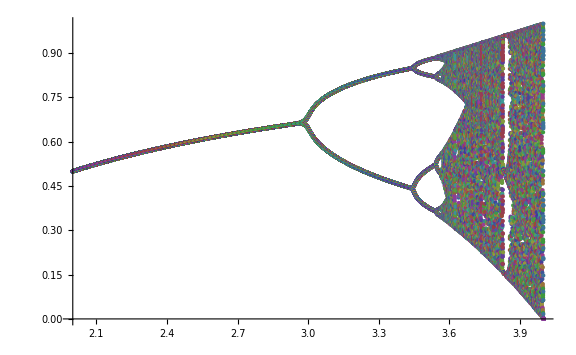

```mathematica
Clear[x,r,n]
ListPlot[
Table[
{r,#}&/@
RecurrenceTable[{x[n+1]==r x[n](1-x[n]),x[1]==0.5},x,{n,100,140}],
{r,2,4,0.001}],
PlotStyle->PointSize[Tiny],ImageSize->Large
]
```

```mathematica
Clear[f,g]

f[r_,x_]:=r x(1-x)
g[r_,x_]:=f[r,x]-x

f[n_,r_,x_]:=Nest[f[r,#]&,x,n]
g[n_,r_,x_]:=f[n,r,x]-x
```

### Fixed point for r < 3

```mathematica
Manipulate[GraphicsRow[{
Plot[{x,f[r,x]},{x,0,1},PlotLabel->"f_2(x)"],
Plot[g[r,x],{x,0,1},PlotLabel->"g_2(x)=f_2(x)-x"]
},ImageSize->Full],{{r,2},1,4}
]
```

{0,(-1+r)/r}

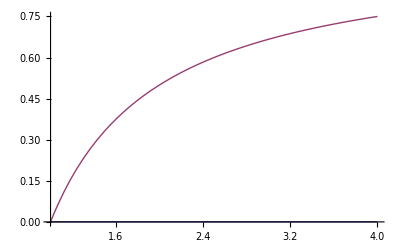

```mathematica
x/.Solve[x==f[1,r,x],x]
Plot[%,{r,1,4}]
```

#### Stability of the fixed point

```mathematica
D[f[r,x],x]/.Solve[x==f[r,x],x]//Last
Reduce[Abs[%]<1,r,Reals]
```

1-r+(1-(-1+r)/r) r

1<r<3

### 2 - cycle

The (unstable) fixed point of the map is also a fixed point of the twice - iterated map

```mathematica
Manipulate[GraphicsRow[{
Plot[{x,f[2,r,x]},{x,0,1},PlotLabel->"f_2(x)"],
Plot[g[2,r,x],{x,0,1},PlotLabel->"g_2(x)=f_2(x)-x"]
},ImageSize->Full],{{r,3},2,4}
]
```

```mathematica
f[2,r,x]-x==0//Factor
```

-x (1-r+r x) (1+r-r x-r^2 x+r^2 x^2)==0

1+r-r x-r^2 x+r^2 x^2

{(r+r^2-r √(-3-2 r+r^2))/(2 r^2),(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}

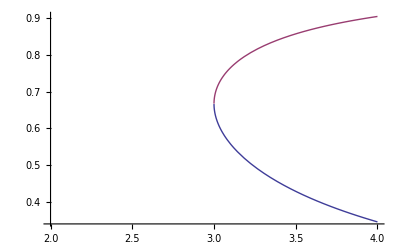

```mathematica
(f[2,r,x]-x)/(f[1,r,x]-x)//Factor
x/.Solve[%==0,x]
Plot[%,{r,2,4}]
```

Using the discriminant

```mathematica
(f[2,r,x]-x)/(f[1,r,x]-x)//Factor
Discriminant[%,x]//Factor
```

1+r-r x-r^2 x+r^2 x^2

(-3+r) r^2 (1+r)

So the bifurcation point r_2=3 satisfies a polynomial equation of degree 4

#### Stability on the 2-cycle

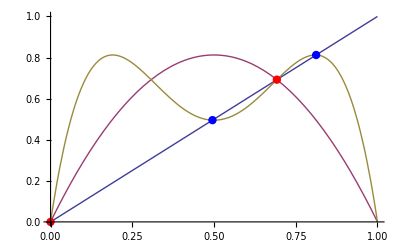

```mathematica
Block[{r=3.25},Show[{
Plot[{x,f[r,x],f[2,r,x]},{x,0,1}],
Graphics[{PointSize[0.015],
{If[Abs[D[f[2,r,x],x]]<1,Blue,Red],Point[{x,x}]}/.Solve[f[2,r,x]==x,x,Reals]}]
}]]
```

```mathematica
Solve[f[2,r,x]==x,x]//Last
D[f[2,r,x],x]/.%//Simplify
Reduce[Abs[%]<1&&r>0,r,Reals]
N[%]
```

{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}

4+2 r-r^2

3<r<1+√6

3.<r<3.44949

### 3 - cycle

```mathematica
Clear[x,r]
```

```mathematica
(f[3,r,x]-x)/(f[1,r,x]-x)//Factor
Discriminant[%,x]//Factor
Solve[%==0&&r>0,r,Reals]
N[%]
```

1+r+r^2-r x-2 r^2 x-2 r^3 x-r^4 x+r^2 x^2+3 r^3 x^2+3 r^4 x^2+2 r^5 x^2-r^3 x^3-3 r^4 x^3-5 r^5 x^3-r^6 x^3+r^4 x^4+4 r^5 x^4+3 r^6 x^4-r^5 x^5-3 r^6 x^5+r^6 x^6

r^30 (7-5 r+r^2)^2 (-7-2 r+r^2)^3 (1+r+r^2)^2

{{r→1+2 √2},{r→1+2 √2},{r→1+2 √2}}

{{r→3.82843},{r→3.82843},{r→3.82843}}

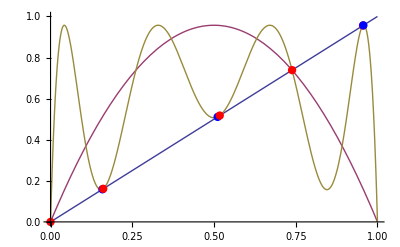

```mathematica
Block[{r=3.8286},Show[{
Plot[{x,f[r,x],f[3,r,x]},{x,0,1}],
Graphics[{PointSize[0.015],
{If[Abs[D[f[3,r,x],x]]<1,Blue,Red],Point[{x,x}]}/.Solve[f[3,r,x]==x,x,Reals]}]
}]]
```

### 4 - cycle

```mathematica
Manipulate[GraphicsRow[{
Plot[{x,f[4,r,x]},{x,0,1},PlotLabel->"f_4(x)"],
Plot[g[4,r,x],{x,0,1},PlotLabel->"g_4(x)=f_4(x)-x"]
},ImageSize->Full],{{r,1+√6},2,4}
]
```

```mathematica
(f[4,r,x]-x)/(f[2,r,x]-x)//Factor
Discriminant[%,x]//Factor
Solve[%==0&&r>0,r,Reals]//Union
N[%]
```

1+r^2-r^2 x-r^3 x-r^4 x-r^5 x+2 r^3 x^2+r^4 x^2+4 r^5 x^2+r^6 x^2+2 r^7 x^2-r^3 x^3-5 r^5 x^3-4 r^6 x^3-5 r^7 x^3-4 r^8 x^3-r^9 x^3+2 r^5 x^4+6 r^6 x^4+4 r^7 x^4+14 r^8 x^4+5 r^9 x^4+3 r^10 x^4-4 r^6 x^5-r^7 x^5-18 r^8 x^5-12 r^9 x^5-12 r^10 x^5-3 r^11 x^5+r^6 x^6+10 r^8 x^6+17 r^9 x^6+18 r^10 x^6+15 r^11 x^6+r^12 x^6-2 r^8 x^7-14 r^9 x^7-12 r^10 x^7-30 r^11 x^7-6 r^12 x^7+6 r^9 x^8+3 r^10 x^8+30 r^11 x^8+15 r^12 x^8-r^9 x^9-15 r^11 x^9-20 r^12 x^9+3 r^11 x^10+15 r^12 x^10-6 r^12 x^11+r^12 x^12

r^132 (1+r^2)^3 (5-4 r+r^2)^3 (-5-2 r+r^2)^2 (-135-54 r-9 r^2+28 r^3+3 r^4-6 r^5+r^6)^4

{{r→1+√6},{r→Root[-135-54 #1-9 #1^2+28 #1^3+3 #1^4-6 #1^5+#1^6&,2]}}

{{r→3.44949},{r→3.9601}}

### Computing r_8

```mathematica
Manipulate[GraphicsRow[{
Plot[{x,f[8,r,x]},{x,0,1},PlotLabel->"f_8(x)"],
Plot[g[8,r,x],{x,0,1},PlotLabel->"g_8(x)=f_8(x)-x"]
},ImageSize->Full],{{r,3.554},2,4}
]
```

```mathematica
r=3.544`400;
x0=0.364`400;
δx=5 10^-4;
δr=10^-4;
n=12;

x=x0+δx Range[-n/2,n/2-1];

Print["current value of r ",Dynamic[r]];
Print["current value of δr ",Dynamic[N[δr]]];

(* repeat until the values of g are very small *) 
While[Min[Abs[g[8,r,#]&/@x]]>10^-300,
(* shift the xs to the left until g is positive for the first half of them *)
While[Or@@(g[8,r,#]<0&/@x[[;;n/2]]),x-=δx];

(* increase r until a change of sign is observed *)
r+=δr;
While[And@@(g[8,r,#]>0&/@x[[;;n/2]]),r+=δr];

(* restore r to the value just before the change of sign *)
r-=δr;

(* decrease the values for δr and δx *)
δr/=4;
δx/=10/4;

(* set new values for x *)
x=x[[n/2+2]]+δx Range[-n/2,n/2-1];
];

r = SetAccuracy[r,-Log10[δr]]
```

current value of r

current value of δr

3.544090359551922853615965986604804540583099845444573675457812530305842942858863012256258566424891799962608992775899745457045376507297519052231468176374479284645609498527555371798891

```mathematica
PSLQ[Table[r^k,{k,0,12}],10^-100]
```

{(2.44302283733265673323146870053445432799153554352008444403166604332312229689776639948649142534298162601015583642786391428511381133330488091600608393514310886378595359817912033527588×10^-7
8.65829368595585413993169692354486866519126271663768328265925399527477822920995365046879226029987916889374091243360992718317914190674655222577469137029999752593804662959342858365683×10^-7
3.06857751825654265155400194467922399141430540739419796322616902616694004099109948917918441957942818616990541505104445187888803092611128412183201629234822727343630272238253838815479×10^-6
0.0000108753159999907773604627846446729726439361362412886128264423784366486519359783947768724017749610001369572105659190946101846328438905571674837118882198103421427112020717452184097355
0.0000385431025926480935728219054015264882214716923225479333012769456728388306271119141322566206106625590041271031534000570906517630010511143462279170379060846422947059834627113134703396
0.00013660023832582483188131525220257356284374881402898694951959851298154481264389424662608369030497447679729493481743352111334167091693323099507115766697017949756823635780043641775006
0.000484123587763050880734775502931793476668120749686746724049488941568340366509076946699505957739055570005812254054445440340053917602692772710287964834001721669062117672423135186357401
0.00171577774022271787489955928942437084133364191493423576082361778811850353656016754854645028969204178640799258925765327962828174387577488965148041363544553825552863264617480706305744
0.00608087134825711787976297220447731365320347230125085118406583614450344268641829121471880524771460507873690863648053980798332245419255320799729528158347704467974287084646321478591362
0.0215511575230335547977961059922751981338463237179929419573100246226158980608484095463995175219659800926783220423906323221881161517846832251564473768925194858573961412873696931918669
0.0763792496145681183512072464798470423293883049810752540140337656272951937601186766227584658928381319229924011181570492323170811959281522920362005859914546282860589994600897310182844
0.270694962228800787601603184348374637943268223288626897226507058851624415725365334983664954269306426147447631121955286731267465966357361628648422151450701090396890272050856993250226
0.959367406014364759483234437532711685535839881557922627353064093091666091873362089747475971855715466942974759467681777970609342886165963055687741499141356068630511496391454475657865),(0.99999999999997015819708135503192618303144094746759540489357162084340526929143589558113298716419848443977190869889542941497715049478749412789033895367200748057237852205920587911499 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.1152409207123928756649669136683013352840867467171440985413554441511029749432553870269718785339614966903747915735268272473252051283597317633297451202359268365521448429338575460013×10^-13 | 0.99999999999962516975223859232515683281608201373951844734228017179984645113822219355299754194812935150723773396150755582168262572019255050237730293920671705251271610906139744778929 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.4966049552265248075093420818131591107819505838399416456507565281922896022547264863183073972493409684253107710308094982884125189330419652081386019755789285705382787655629929766632×10^-13 | -2.6568645351198252418886464722121470666103076809192926584911201057633477310228093095973138836368518585740999505943542508703657366693063753147407775843573639815597094100755788795535×10^-12 | 0.99999999999529191600721036533755053143227160785574300946059076361847378174593458959780890827386628136038962503916992401753596053104887217259693755550053491140240822952275019889962 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.656864535118750083068840457505541127209232242715849878910039274373111981603451266707070287703913235855209796826058448882556372072306625229493661906651061974785461964229692718035×10^-12 | -9.4161679855535738054367857427414272085377413687868229389732545720917002779780462046152190761095143476443820253402004861993121808244822513346338668727007772138665223841490429386155×10^-12 | -3.337175018169149625078805722569396582630103953097077499320304812687187951410661383342272852276334342630223160056364337159615080827124984604159094853930903652564961494708771193342×10^-11 | 0.99999999994086375094781905271390080111099900812642548763411298099434800254271060048714920588101142026966666229002882197362746516078191453062619451919970400874385537502367854476412 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9.4161679855497633454285240230456151752876230968837627633981556261254082205462335221571931929118159676832455576888971682515483456968330336829540821145156182655455006657506581817206×10^-12 | -3.337175018152187050655748457709936609540812805748896066767555888653640322960308243310960713095740091583671757078069452989094477802390980907499617636089575146923921806377299257516×10^-11 | -1.1827249810030796176514090176789068708482513448820581645768283401162993761522396494683388691676427719519258870218069535105012315435899973129619981076315487722676691044384652313076×10^-10 | -4.1916842034418608510885911326526480183365548162205171911386171778866670156339847363124322011691843217578488224165303148316389261703478850603394871149755689211732719867587843030747×10^-10 | 0.99999999925721462089499040081999423769814881591294246140310697502611536859397499595735811133883910412538371999981378800913933351330130952621976177837837813522825356821668003679737 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.3371750181508365891976746076015328930026590503051254894253138159781309676854060508358245677197267426283010185679453657596034771150280496489657755441120430524418507038051841017057×10^-11 | -1.1827249809970679280028150904615500164416891563658434417940336189019698677928465028622462104538866970873906001890204861184370395291011970067363337005987276064873865598109767805089×10^-10 | -4.1916842031742455687858737864874998676342916817124034203112325298476598068556011620826516135940561010754415428688552575803851174368783095523053187726204801506371394854174573067142×10^-10 | -1.4855707575704379966383209644597803363038864784068558416289064579282934007132300007437356317384690907304275551666758432170159812288398574423919025335204899172149873000607767608762×10^-9 | -5.2649970045597509889678751349593561596790476690043998717576940205851805950975153709058271057522659390538572805082517331341619765594513094697214522107700492865705653770817956793381×10^-9 | 0.99999999067018738608226758227228144514043600505793583965067346595807671998492884705326815904728789102309452858513144566627292110181243002801149075835896804576097861176982562139545 | 0 | 0 | 0 | 0 | 0 | 0
-1.1827249809965893122593644939194656950193333222858417603904829917564644300123717461988612529992712207348523362248309629624156054817155808037011566096780131157591110416748148377296×10^-10 | -4.1916842031529395974576739622246122183755919677668734028742396627008926149010572258549411488599210126561060895784882380244528892430592697215648310951728367545467569620480972089847×10^-10 | -1.4855707574755927224305382788272078101586121174597934836540004558253859767535302159711291154515675980626280072924251156636253287032386645537494214819971611630109583175513213390582×10^-9 | -5.2649970003376360190598562850118373935739997368679414017152139036648846283566854579689757438099949318922261767060974254814202000514125255795534833669065555142404894343964513329849×10^-9 | -1.8659625126929964690477892475710986800548534637565418114972863727166047150482868104794658355589780505984709894371914870057532602784898303947871070193788427857180056042728732274786×10^-8 | -6.6131398191320300914579349671750655478773954578152139675734080059714446568239074286277524074229197069943564689678101833888250213659120849837418706324386575074251065440695831703001×10^-8 | 0.99999988281216664339152182895594852536952569440942941417658182016561776707376917318092768415592730599843930920995988606300971797903707868950775128231872843497053972746355713246953 | 0 | 0 | 0 | 0 | 0
-4.1916842031512433400153809266601016567308852371743735228210405234110129827341320938015242375372886108207753524266352921920196406849021728412555224869857994988585763396111572688916×10^-10 | -1.4855707574680416936720220113781963702337170165572254262992581856227010309374819339926138000604780203661962114098675599397092939223244830519530532162928875994371881741085674546789×10^-9 | -5.2649970000014957970909950317015610897337258191429429655636247084847167018920203388035730458427158925948359278493770562340069404955086743223225242705840452263428442040251732582238×10^-9 | -1.865962511196640772870702601033539576138493735750921441221109111362761101132552040342859243752820265020854112322869768784405507529035202469214185770898317848571388164260781712956×10^-8 | -6.6131397525205312675192485469948987194683101843387815812005752588456692473482168823070283971271937217451510805225205889015995276843012483980295275545103338976696012622927913472833×10^-8 | -2.3437565079354774595570678796220625239585562238469275049843226602177342393866951208947208936652107533032612263958803896559455819316756552949024714675320464418580994966466542233311×10^-7 | -8.3064858958282381842673988961967830882036110664278998003753123683502115295569295853886562170229986085741627331432363583692562574253880550029887138920187003932198757415802284800565×10^-7 | 0.99999852805191493219364811166677011049555508940810588285560583470163932284419041372234230350518117047343847306330778583159585087668614524306194314250471502455967655610567022151821 | 0 | 0 | 0 | 0
-1.4855707574674405247071671164336920006318716951609862651207339174922727808399369690809178570466552033976717131160324607690665945873320822752789693836442248630396356180025694326885×10^-9 | -5.2649969999747342688632382037507175981587072569393388630977828677470190470578422823755516936597025443589989443308956687870429160722393666675389755969543423615870588856139368876959×10^-9 | -1.865962511077509640856954137374563055376769688223523096084659564511947706901420631554013761442219697970501151257005920565377910702761812684961493875764298800226663212394997866893×10^-8 | -6.6131397472173114702374297004349316999930100114313308921882245889608229980447979485113630872408194839507387888420236523791146007404185686102797567205864170045908311196536340520927×10^-8 | -2.3437564843277603778345333332791070841598951034666049164589652553983859789715609236024443971361786117909013886140683736209623396594523122657615003239208157109780803616037267499252×10^-7 | -8.3064848449112054385187568316449611510698062303479335814005058799261070872585453155047250542416402846707615588522648116580856398782329505807596472237382680943269257231634303040842×10^-7 | -2.9438936585158876667964048702685397629296158185818735283893935606537773784417716968595498715018715702414435088913834793790216365376598757484545437670713845854160053044495496508842×10^-6 | -0.000010433441714847380058222554351002766029063191767618262785094367001047821153939102911756042589495239060862508507033426026907596842810948276763493804733654103919695507700819611286388 | 0.99998151127176999894448689699653241961237006572935643192999418734040073869468964982824232061703860787890675997237828047313828776570373110649628402905538671103978297113499459865635 | 0 | 0 | 0
-5.2649969999726036717304341618533537518360954219970343575197523347261954898954447092165641365308583913357987345637651162582508382175814750065170570433039046891767187018718776536547×10^-9 | -1.8659625110680251134370671744582036635948053626174766360511362663215758927620833007402813117799940862066348063294682228511068176511861869772916416976394289518812159635771625948498×10^-8 | -6.6131397467950999737449963205945627364007955504317897610618772524071894100905437603015683822943256226613873818445023711162895928837935497403617614820701340927185804682918164160326×10^-8 | -2.3437564824482513620213936548844925295081201141458082808641352006616024668839448964094004229877212680102151025921764037814035758689052783506298656002510669575407036776915909665713×10^-7 | -8.306484761243322918156668453803767904373783715630149753741041021685183590080160933773452567512399208933221434373134962934936097276638141290214935630853152558554073712631305753268×10^-7 | -2.943893286061395222484386049770826878184354184518953301011021424686892997804506770475892065297602125759070436421328461484569654500764544085204045221427058290831623790412042791351×10^-6 | -0.000010433425134692197916970177745292528955956393807774478978447221449210088441999125748506753000675422224957690495316497719436043051485134336351269432896817865827253920606041783034608 | -0.00003697706019853748174504983723262159359241719399899104035580408421070990676342541726708083331022300150447603351483396681424738034613242988649658556095396358364095156604373815585342 | -0.0001310526584703372294307960187618487737926362503742540470193181208473622755143037979959430314385335371325400629992416193383918187285391082674731116300262421222169568815354735813193 | 0.99976773750158721318811787522881080586402151453571725983599156730381120252135882393730383956763851659428149900050219798740506558540673795071800418625512850006607079126704114018382 | 0 | 0
-1.865962511067270010561221197180791415862203782158284790796750250587838526148916505328584005095688362362876046585135902112472833373096955177893417244417362266882007088959470612245×10^-8 | -6.6131397467614859515512690630141200048072586837136638691976637357473442330363188897560825701062621258955132288177094654349905697034521726983657304654553551133968134710128325961642×10^-8 | -2.3437564822986157925803112916929317447304430041293064815102249456346226246529442186490294386394306281068314980187494512085709886808879597358174474593360460881659379309678950782881×10^-7 | -8.3064847545821731345223975946805300722663254883135326286842301942968183097840238057239490292595860019913371646005239028767333005855010342014066824481342927989912742771706657210425×10^-7 | -2.9438932564087416380305745412051702348846292395526044159865786615658123331888251087348247608661286868241772892070775401318383867063615020091245841249831545226540954383367002384962×10^-6 | -0.000010433423814679821873279461143789101186129470348923838555491042797434407812514580153552281637335290684406241059284248403145035419067028082889541405842452875952176621663990625652361 | -0.000036977001436969340843381751595540492516361713873230421297329172867657902257987503179116513339153043039005352068095896414126575252210496982720614772670692210555521329265511908046146 | -0.00013105004257420779953587578882975414454525279937905665646947540257530827714622135875235045103162377613606325421505741942366864222578361306392238083966558300378359483321759612896617 | -0.00046446246347837281954136234740087562712772978798292520428234396143280224432808995896340385893487528263580321077843226983984957079710418819099642111006149047656330713924800862907448 | -0.0016465097964680766171196989892255849792481484595126350771962626772217042422192936165111674622834219755967892879531771629372878195356198367448948416084576465993070568919741335636678 | 0.99707736151651787758364094094491828487760131415291283884672577808057392314776014430882811935832651179769547859228678908477028552121867456669841308613333047487305878876065764596426 | 0
-6.6131397467588097987285134024422996548941946795686251776294236354256652867549074300874341437764600879034934479840232287765179180457385682869864904731266824316327476217358089183207×10^-8 | -2.3437564822867026793800559766012288334260172489341428049823384705909546287452039904630403761143827503081176742685178059778385836199330253045205437964431373252849323050327329654968×10^-7 | -8.3064847540518511554201952822800108103106696318504475505539754584500995277202033149622138316677900974638341195533924766562273637484770918508207917092968392961727243102360651673593×10^-7 | -2.9438932540479699648596149281291586775669466589426655207784429835024873964147712054412800760157069389713875326183502524520511595700920895854459893413418136438788731335443797168068×10^-6 | -0.000010433423709588138169483938311860861442976236266181219884075595969068017820647820030155919891814954507667879142373507554499296474941809207825945191123770267735644909225612149312776 | -0.000036976996758726204417709922715925590755244797412482606260668634621052806161840945341174468509099757292445231695755913892435804248008047409780992551485356445765556997020141010808597 | -0.00013104983431790063921286798822990670468068778780322747695192745024807018997806205675275099917025216222079859267878644638538509228531823616471144154901275685485245050855893937235909 | -0.00046445319250611891786175265951656774345016182051634643109376670388243004074369655840274577338014778221632391114815283317892665472995723047549137215356662519838587758719437311100111 | -0.0016460969391874381629846740070653287868522618038102167879595407266266739992916545387662867886542596850121997335921421420760447878405079992196076492818446611152145218089006640328827 | -0.0058353794965703089753805637378756682417293073251669041435884125156831511557219324602858343127761761051727592452201183131634913090262643223455387312380468291973138575096188209680509 | -0.020746551450504045669930373354505129779629551341227794606500178177104800614032907783711599346614147669252194902400683975422476597539208367434791167905773881916124131558657087012506 | 0.9624223721222714775143028667232049643836004134974058060203635100190325678768425000881666262298914855092055248548216636367320307831990206226302459710751513390050151937433688408572
-2.3437564822857542266380743763664375678434803242093884249444140482781644113861893217223699784378709182066143419953059882811854104961192860419077605830430427221048795854807540486464×10^-7 | -8.3064847540096300057749196642920643751046655858282328444373779211874031895473773971791310667783210934227660855477329792487368782563791204279450785284021662294819780887475438544917×10^-7 | -2.9438932538600190635001537770204046132859438730212633982509773079156947824694133886119544120471213712346707144203873049705013420711826218098561221067468567899686034411577270093574×10^-6 | -0.000010433423701221350041495477549787543909303947815595244588999179889378102124555688895449401339011592372149806354490527629002684408565267363877851182678686941105630613553795412030479 | -0.00003697699638627178133400829657881900437510184202472248053751480018017320581733601172832181781940282358730697286029469147678150022946885425000880162205470163592623717256166258675055 | -0.00013104981773778423976669343763440209237382219833134855802858444127155906597063670129027485256206221103038429286524830269115712613120727757537602135312463822788874758331066997092982 | -0.00046445245442694839507689805608024944142542003287267026169587220936590410765202312967840083824564468273315537843450926869915652504739834986465316756700792101389755211878481338398113 | -0.0016460640820240494366803732374925912777428103474911339633246165454638113193476236332221768107210554921153229235766641754590237472462406249389119691971243617787143249807239411210783 | -0.0058339162930621274073474919110674491998400942480702059958678197503663866226294924939378761778153150746991131542164033119875439803043990347465165524949734831924736803406239221394428 | -0.020681112218121784908976608232992084457048187402238762009768951678087621488192604097622940281544581443101783531925313921439613449999719879416099444959020444465716698041904666494353 | -0.073527652989679349828548583614019450847975975159543265275991629646351529773785991461661513911188105189794606572212150148774595333176009805571183563790357098934271483403641531942554 | -0.27155695100391005301594054838903439475849908172329228983272430812956463774849717707344586607881341611741901996014090886878073170482761551818272025350441446072761613242027590916761),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

{(-2.5660602608275399712509501248495275×10^-49
0.
-1.6796005483193085059621223790925376612×10^-48
1.32056873405320059240890852744318712213×10^-48
-3.0324563231804911945851123813872818367×10^-49
1.193358043143288217933591357579782554×10^-49
7.7240320618545082570147460268116922562×10^-49
-7.9368288796531193884437302825885740256×10^-49
-3.9176131195110672219806123430054685275×10^-49
8.8523366728837643565775611683760085605×10^-49
5.0816362716987543239919174633411074484×10^-49
-2.1738060463629030531782825785748290887×10^-49
-2.758522533059692295574704826803344749036×10^-48),(0.00020143182752552829625456048307512439119315359 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000063385413000783560961101118621270100802066423 | 0.0002436929874873499788732180061270217051278868 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000088197855887746938228577132763587882039082442 | -0.0000763965669817609684763711908201563291160982 | 0.0002878200931878228276560523201739585306189023 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000068094797047250508373271674747943785580937963 | -0.0000902080308792486914059632445076998964028596 | 0.000107473803262441788242765799083080148107703 | 0.000195031714841228278881643325311972779869222 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000081911823677798613980605636955667180242077246 | 0.0000133990945172407044806843598869632044869684 | -0.0001067148533170672261088705578414470037266907 | -0.000076759675902956587993647021677676619631224 | 0.000144475952127659438773706861133250855174 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000091176516930857400488254185580398230197058489 | 0.000120718461272476799350863648875391294449474 | -0.000134870904001842848247310035775191270712077 | -0.000069544325923620493615778027054535241385293 | 0.0000192164824392750561094056659230102485332 | 0.00012545579565081367939388982582422628135 | 0. | 0. | 0. | 0. | 0. | 0.
-0.00002777172903139179180252293345877480797184929 | -0.0000318333384578397181424341064516959416823821 | 0.00004947235075064241586025382186625240638901 | 0.00002990658902199377098829632871521329962988 | -0.0000359394811832965269106628210177794011754 | 0.000041379832681101516565044136145536921475 | 0.0001074992208868048003551654725015544343 | 0. | 0. | 0. | 0. | 0.
-0.0000286490184824094211112917662894651388807356 | 0.0000639012884885467929464102309486749601932586 | -0.0000323868587214316616276080640653835997951867 | 0.00001432026348188373683655409785052696770795 | -0.0000694037802730431519972299593649531739098 | 0.000062146594433968280719003809626960085569 | 0.00001177933763202365775567050509037809692 | 0.00006409549568371092887774865490153883459 | 0. | 0. | 0. | 0.
4.9857359673454713837828755227282642640598×10^-6 | 0.000033819256056284345159285486570584868370609 | -0.000137632674102969139060618294172022659325438 | 0.0000202420356604628794851974868697524080417 | -0.000019997827955371604466169268392725648743 | -0.00001808909516320962067635037653924248624 | -0.00002224609528610586882557556127083520092 | 0.0000251365775034153540963742001104768351 | 0.0000662814278482566622332011747194561374 | 0. | 0. | 0.
0.000035808064438763067880088836620920012703252 | 1.48859468217458261661673608528422999334×10^-6 | 0.00010231293625232758350902232917469339617416 | -0.0000717008916026156557857889782323985294021 | -0.000066314712624253279188197353631506603067 | -2.155914103332908448887180156425092×10^-6 | 0.0000171945219176268603682920552688801476 | -0.0000262786508911973790170370012741308354 | -0.000027934432210644518676883076999956338 | 0.000051978075095020360882712501997125155 | 0. | 0.
1.0172092576417338122256973526356867556×10^-6 | 0.00003240861375491319607241362309636476624225 | -0.00005963622693351696174554693839962542786042 | -2.7987507912135373544010496937815841147×10^-6 | -0.00002895710970498930967103843464849824353 | -0.00003225494369751589230847733296229597386 | -0.0000277948075720550190360859835102994754 | 0.0000317449843902313963974307047979319727 | 0.000014279591959616871524835933135556722 | -2.098893070852320581796925172948189×10^-6 | 0.00004425414474940796697910543143535441 | 0.
0.000033953091243475425876758668461661544687885 | -0.000041356889511906789665445175580304000546 | 0.000118758099117536624513675570090796782369 | 0.0000809720735739033493638092078448613622017 | -0.00002296540235166319217583690030635637246 | 0.0000502581261569690015489694849702602324 | 0.0000278023988143241814409568078898750544 | 7.2916067270058872561002372809662388×10^-6 | 0.000024774940111975197022156740936899418 | -8.651861338958103098225648446845421×10^-6 | -7.28219925264748648082834684455148×10^-6 | -0.00005257677466166608759849459862749907
0.0000813841096122998613562043692557487322802 | -0.0000153144158028852357919905065673650064194 | -0.00006269425488404191322944953245379835320525 | 0.000070269072181648474187427516937772330095 | -0.00002711089784184871633804433586397478019 | -8.8921571854817490779648017025567615×10^-6 | 0.000028077349345404489083921202073007465 | -0.000025171152250911543508118980891161376 | -0.0000176994099677636670856752694680523 | 0.00001697535807916064049751546359944199 | 8.72617689407919621416362162037824×10^-6 | 4.14322193449765934619255188019638×10^-6),(-234635648219154506354039589917187484 | -831569938860721781625903654272515284 | -2947159003609465963678932418945543784 | -10444997812758958930345272013217058836 | -37018016053739946534744078880242187221 | -131195193825798059462543739884019686303 | -464967621657556853779144217121904998809 | -1647887265420333101557305342733421832797 | -5840261371004583269766014746080686616294 | -20698414022240839432938372479182488513661 | -73357049594238098342823801511928133829079 | -259984012272111538432195542800552454054147 | -921406831531219305877954319688593118497007
-1323114352580451231108659298283260237 | -4689236821565161029178324293540456305 | -16619079012964987461632722806359696355 | -58899517714480897580633262566556563880 | -208745212914149453698769206923100010006 | -739811896691650627129174597997744957323 | -2621960210946702076565907580643526161455 | -9292463906744932854095736833857343017869 | -32933331748378914796837085558308624959446 | -116718703557354984247999339583147520435259 | -413661632057020523151662687886865933400998 | -1466054202289801082763292548087842147782632 | -5195828564915868560332611868305427807858526
1764099846495330050859785330411282818 | 6252129259251126193116334965583304979 | 22158111034384420922857732096461570274 | 78530347702842911565334844470764247535 | 278318648225906053369799899958766310201 | 986386438060956520331027565433844157425 | 3495842665924595875686073689321197976632 | 12389582290813653523959725288198923944024 | 43909799155747897332887746521874104722909 | 155620295877747284023753589680717360002879 | 551532390370941989728427053476531887591969 | 1954680627694283270299960572708707732554789 | 6927564768614210647629957719486181815546028
7052811583599769961328575545229859841 | 24995801541172075129798532513682307990 | 88587379271341047142564704920944205837 | 313961676853529649340726493592535625628 | 1112708552205350509964173333220587336355 | 3943539652861960209955827262159181859016 | 13976260866218809596501352202929306867011 | 49533131398548889655581760501136562329243 | 175549893468015773648523855318548560289070 | 622164685060361776402505743585469000007097 | 2205007862376086413197827942191479059400544 | 7814747107783280920813563185228149455142392 | 27696169887030997296858857045033076014668032
-58017326816808950059791374357398501107 | -205618648658425847627722387437239533003 | -728731070454420962018031044541653115235 | -2582688761503466412339430585724801447376 | -9153282341367530608303372757177668191068 | -32440059704297517814325586738869031168556 | -114970502861289634076850259822421270435765 | -407465850823533354459268428247714266092265 | -1444095793750306486991604928089910928849681 | -5118005980899943145223588555854411453224254 | -18138675657036571110436934831910272860407911 | -64285105531142451812363546114685297506273285 | -227832222775699956613571381594286918010002766
145122322647146824219574213715317771905 | 514326624649536745012850872094350747853 | 1822820032081303550183526259119527682336 | 6460238902897474650092567818409135979657 | 22895670416161230563168019667677731338933 | 81144324797395178780038276898622709836853 | 287582819246798288724334176929313179155244 | 1019219497265340986935228622765576592323323 | 3612205994525452390036405958131353670053874 | 12801984441913321635988720108685709618470574 | 45371389643718706508901730603246474705089720 | 160800304635777419490832285920768002384713429 | 569890809472671121884252310947413041161323870
296619330160646328405801705295244861355 | 1051245708479095560851669951648800352391 | 3725709780941093661529421617480791107638 | 13204252117121636366784356288991943312383 | 46797062633383858786170658830122948342919 | 165853018534323253819747185729108508033536 | 587798084090081425722361311625233220033640 | 2083209523186748064348590611523537785675858 | 7383082788052911716136937454260235996826473 | 26166312532912056915904149978485093310971898 | 92735775992916276992287209073108113379010977 | 328663969682061223700839958175780028186285326 | 1164814806482258634193563755825046442771570617
-812093999795812148666453396516925467718 | -2878134515726299042435560529662558201739 | -10200368790679218534057067253130899801570 | -36151028694920524119092679534646670589165 | -128122512285552760720156539703128135298777 | -454077760632800336847229629397608975446831 | -1609292613945633306404221688522776084572002 | -5703478438782833323168466077239559728836250 | -20213642950802491370815447895933981990029772 | -71638977113363792479868889056203112937392624 | -253895008155633455666116653277511384873494487 | -899826850742737359184244127916285626088503242 | -3189067666983302467176199224652368833095354443
-2676282627915241920790414340298058302861 | -9484987461030694705707765955510650114754 | -33615652621109754655574952596267915488415 | -119136910384521408276484477546076352636341 | -422231975560583689452206110525786218052519 | -1496428274078827751039517827225325610967789 | -5303477019923696001742008836953498605626314 | -18796001778416732086343686318939047861768002 | -66614728701007537409611148619171651446074433 | -236088617793407598077248176868466724584664751 | -836719394321554425741708845397812781350096195 | -2965409139065144941954746748444201146901420435 | -10509677941887947535891132280701040790881152671
12875803824987168908920268691673825522802 | 45633012207618799018495161528843058005187 | 161727518642336994265328543939456834851171 | 573176939694560424202097151587375642675134 | 2031390866288965456340691019586773736018668 | 7199432785696551625632693478131037277125420 | 25515440330029193203448590315363923424349242 | 90429026093378796459108091751500057557259754 | 320488639601213072396918599742115697625713999 | 1135840697956569859106888632919607833567457415 | 4025522067614606677640052897291862501187428521 | 14266813951996451280653029639515700296661753919 | 50562877788791492454369564137891047311677607729
25217202564116848565345101849187995630835 | 89372044502354552749301782513953914293303 | 316742601334240197033790020926933803902326 | 1122564399848078699287853735462343405604157 | 3978469667477765729751188440013561065609504 | 14100055994277693701570678188579445126103202 | 49971872518461876556998315008965262510486613 | 177104831641438404695628590041915000962707890 | 627675526450488199042835525110190700596267162 | 2224538782219853184774443597542047978978182882 | 7883966452514756083216718412350597703179600574 | 27941489499388319602049461809160049109802380885 | 99027163566303426517617164495320303947287891819
-67287889692080631288324371084380798517609 | -238474361172296168092233637712323119644342 | -845174684431038237160786879005620241805683 | -2995375451229381240317052474692359123270744 | -10615881259940540918036859625503065087648931 | -37623642431503191459494083133186637002009227 | -133341588432719126823546101588787732011283274 | -472574638091740047523700054931389205232172383 | -1674847219029674802765072734650330111884925827 | -5935809882685418259882543749294238224156147517 | -21037046581358421013705868112448964490846009508 | -74557193982437115818973315533253268074979448922 | -264237432428398016758175537265444709311902546145
-73771084855240579053455030722295559061040 | -261451390649144994516577271481256454908262 | -926607353091078524268248164709904099328517 | -3283980187180016021270610890770989080114968 | -11638722522344213894577399551054217980046093 | -41248684288939967490182236110214894789973413 | -146189064332633000652384099868369906808141242 | -518107253573200472251270036672881177530605227 | -1836218922602703328351224857078124981088726935 | -6507725781623059240973305988591324848244756970 | -23063968205257786211962943089020450391064553429 | -81740787369266184371054783964207162627411580012 | -289696736497599865555833040240634563835722792048),(-4767 | 4913 | -6998 | 920 | 523 | -3491 | 1043 | -4311 | -884 | 3190 | -1995 | 4152 | -3836
2349 | 0 | 1912 | -4177 | -5606 | 5330 | 8941 | -10488 | -3403 | -5166 | 13224 | 1865 | 2207
5852 | 2108 | 8279 | 2184 | 3043 | -1926 | 2322 | 5260 | 7766 | 507 | -2861 | -6934 | 5099
-6655 | -604 | -6156 | 3913 | 5491 | -4387 | -2145 | 3133 | -5071 | 8343 | 7391 | 2426 | 1898
-4102 | -977 | 295 | 2178 | -4624 | 2989 | -88 | -3153 | 9070 | 4601 | -8447 | -2329 | -245
-1677 | 8 | -6281 | 3902 | -3136 | 3691 | -2009 | -5581 | -3921 | 163 | 1299 | 4642 | -3556
4495 | 44 | 8452 | 582 | 1211 | 1854 | 4880 | 2589 | 4396 | -6843 | -2227 | -9774 | 6794
-798 | 392 | -7110 | -913 | 3705 | -6664 | 2667 | 1400 | 3661 | 4884 | -8606 | 3438 | -5379
2998 | -193 | 6181 | 7180 | 9695 | 6390 | 675 | -1919 | 11059 | 12045 | 8200 | 1050 | 3576
-1556 | -40 | -258 | 686 | 416 | 956 | 2134 | -8315 | 661 | -537 | 4168 | 3951 | -2195
4251 | 48 | 8706 | -1579 | -6141 | 6688 | 75 | -8285 | 2705 | -4554 | -815 | -9683 | 7770
486 | -12 | 960 | -4223 | -4425 | -1393 | -649 | -3230 | 4094 | -5381 | 2530 | 2214 | -2209
-460 | 1 | -988 | 1257 | 1660 | -191 | 118 | 1767 | -1464 | 1811 | -778 | 49 | 38)}

0.

Norm bound 3474.392593387945846861466969341127386976532

{4913,0,2108,-604,-977,8,44,392,-193,-40,48,-12,1}